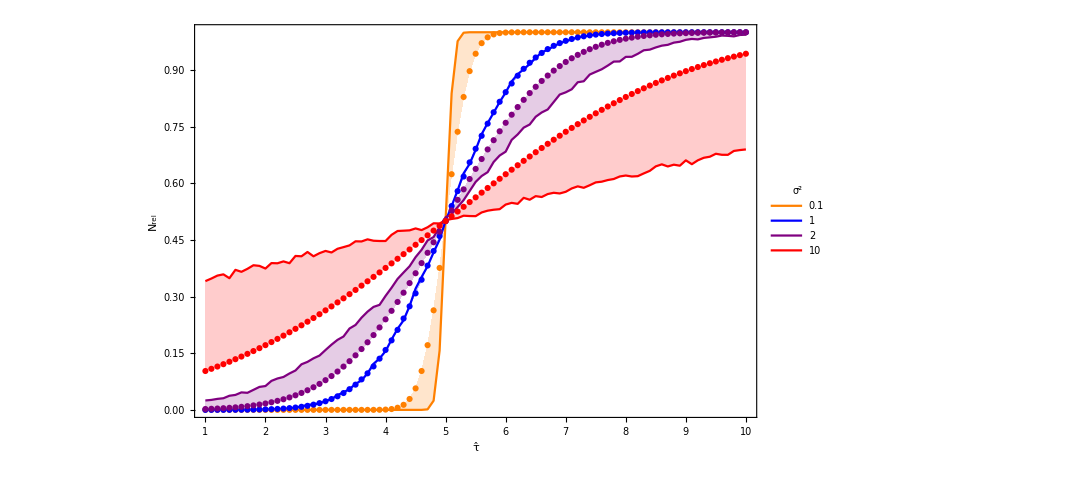

```mathematica
dat=Table[{μ,Count[RandomVariate[NormalDistribution[μ,σ],n],x_/;x>τ]/n},{σ,{.1,1,2,10}},{μ,1,10,.1}];
cdfs=Table[{τ,CDF[NormalDistribution[5,Sqrt[σ]],τ]},{σ,{.1,1,2,10}},{τ,1,10,.1}];
ListPlot[Join[dat,cdfs],Filling->{1->{5},2->{6},3->{7},4->{8}},PlotRange->{{1,10},Automatic},FrameLabel->{"τ̂","N_rel" },FrameStyle->24,Joined->{True,True,True,True,False,False,False,False},PlotStyle->{Orange,Blue,Purple,Red,Orange,Blue,Purple,Red},Frame->{True,True,False,False},PlotLegends->LineLegend[{0.1,1,2,10},LegendLabel->"σ^2",LabelStyle->24],FrameTicks->{Range[10],Automatic},ImageSize->{800,800}]
```